```mathematica
PrimeQ[157]
```

True

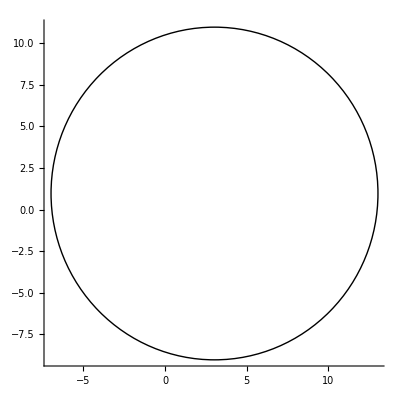

```mathematica
Graphics[Circle[{3,1},10],Axes->True]
```

```mathematica
circleEquation= x^2+y^2-(6x)-(2y)+k==0;
rsqr = 10-k;
c = EuclideanDistance[{8,1},{3,1}];
m1 = (y-1)/(x-8);
m2 = (y-1)/(x-3);
m3 = (1-y)/(x-3);
Solve[m1==-1/m2 && m1 == m3,{x,y}]
```

{{x→11/2,y→-3/2},{x→11/2,y→7/2}}

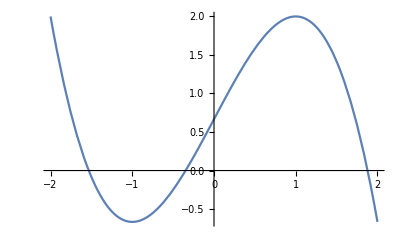

```mathematica
fx = (-2/3)x^3 + 2x+2/3;
Plot[fx,{x,-2,2}]
```

```mathematica
Solve[(a/(1-r)== 2) && ((ar-a)== -4) && (-1<r < 1) , r]
```

{}

```mathematica
px = ax^2014 + x^2015 - (b*(x-2)^2);
qx = x^2 - 1;
Solve[PolynomialRemainder[px,qx,x] == 5x-4 ,a+b]
```

Solve[ax^2014-5 b+(1+4 b) x==-4+5 x,a+b]

```mathematica
Solve[Sin[x+60]== 1/2,x]
```

{{x→ConditionalExpression[-60+π/6+2 π C[1],C[1]∈Integers]},{x→ConditionalExpression[-60+(5 π)/6+2 π C[1],C[1]∈Integers]}}

```mathematica
Solve[a == Sin[2x+(60Degree)] &&
 b ==  Sin[x+(45Degree)] && 
k == Sin[3x+(105Degree)]*Sin[x+(15Degree)],k]
```

{}

```mathematica
Sin[x]Sin[y]
```

Sin[x] Sin[y]

```mathematica
fx = x^3 + x^2 + 10;
fquote = D[fx,x]
```

2 x+3 x^2

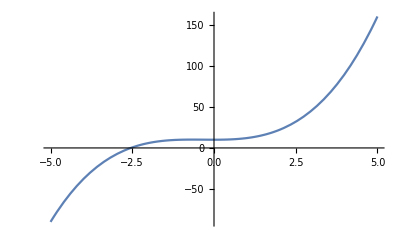

```mathematica
p1 = Plot[fx, {x,-5,5}];
```